## Definiciones

```mathematica
Get["/home/jadeleon/Documents/chaos_meets_channels/Mathematica_packages/QMB.wl"]
```

```mathematica
DimH[xc_]:=2*Sum[VerticalBoundary[x,xc]+1,{x,0,2*xc}]
```

```mathematica
TagPosition[ket_,tags_]:=FirstPosition[tags,Tag[ket]]
```

```mathematica
ClearAll[HorizontalBoundary,VerticalBoundary]

HorizontalBoundary[y_,xc_]:=Round[xc+Sqrt[xc^2-y^2]]
HorizontalBoundary[y_,xc_,yu_]:=Round[xc+Sqrt[yu^2-y^2]]

VerticalBoundary[x_,xc_]:=If[x<=xc,xc,Round[Sqrt[xc^2-(x-xc)^2]]]
VerticalBoundary[x_,xc_,yu_]:=If[x<=xc,yu,Round[Sqrt[yu^2-(x-xc)^2]]]
```

```mathematica
Basis[xc_]:=Flatten[Table[{x,y,c},{x,0,2*xc},{y,0,VerticalBoundary[x,xc]},{c,0,1}],2]
```

```mathematica
(* xc: length of square part of the stadium, tags: tags of position basis kets *)
VerticalShift[xc_,tags_]:=
Module[{ymax},
SparseArray[Transpose[{Flatten[
Table[
ymax=VerticalBoundary[x,xc];
Join[
(* y = 0 *)
{If[ymax==0.,TagPosition[{x,0.,1.},tags],TagPosition[{x,1.,0.},tags]],TagPosition[{x,0.,0.},tags]},
(* 1 <= y < ymax *)
Table[
{TagPosition[{x,y+1.,0.},tags],TagPosition[{x,y-1.,1.},tags]}
,{y,1.,ymax-1}],
(* y = ymax *)
If[ymax>0.,TagPosition[#,tags]&/@{{x,ymax,1.},{x,ymax-1.,1.}},{}]
]
,{x,0.,2.*xc}]
],Range[DimH[xc]]}]->1.]
]
```

```mathematica
ClearAll[HorizontalShift]
HorizontalShift[xc_,tags_,reversedBasis_]:=
Module[{ymax,xmax},
SparseArray[Transpose[{Flatten[
Table[
ymax=VerticalBoundary[x,xc];
Table[
xmax=HorizontalBoundary2[y,reversedBasis];
Which[x==0.,{TagPosition[{1.,y,0.},tags],TagPosition[{0.,y,0.},tags]},x==xmax,{TagPosition[{x,y,1.},tags],TagPosition[{x-1.,y,1.},tags]},1<=x<xmax,{TagPosition[{x+1.,y,0.},tags],TagPosition[{x-1.,y,1.},tags]}]
,{y,0.,ymax}]
,{x,0.,2.*xc}]
],Range[DimH[xc]]}]->1.]
]
```

```mathematica
HorizontalBoundary2[y_,reversedBasis_]:=SelectFirst[reversedBasis,#[[2]]==y&][[1]]
```

```mathematica
Coin[α_,xc_]:=KroneckerProduct[IdentityMatrix[Round[DimH[xc]]/2,SparseArray],SparseArray[{{Cos[α],Sin[α]},{-Sin[α],Cos[α]}}]]
```

## Vertical shift (en el paper x_c=m_c, considero 2 x_c=m_r y y_u=n_u=x_c como en el paper)

Ejemplo para x_c=1 (en el paper x_c=m_c)

```mathematica
xc=1;

(* Elementos de la base de posición *)
basis=Basis[xc]

(* Tags de la base *)
tags=Tag/@basis

VerticalShift[xc,tags]//MatrixForm
```

{{0,0,0},{0,0,1},{0,1,0},{0,1,1},{1,0,0},{1,0,1},{1,1,0},{1,1,1},{2,0,0},{2,0,1}}

{0.,14.2478,10.1489,24.3967,1.73205,15.9799,11.8809,26.1287,3.4641,17.7119}

(0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0
1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0)

Escalamiento del tiempo de cómputo:

```mathematica
Table[basis=Basis[xc];tags=Tag/@basis;AbsoluteTiming[{xc,VerticalShift[xc,tags]}],{xc,25,50,5}]
```

{{0.002902,{5,SparseArray[…]}},{0.014788,{10,SparseArray[…]}},{0.043296,{15,SparseArray[…]}},{0.11089,{20,SparseArray[…]}},{0.23153,{25,SparseArray[…]}}}

Memoria máxima que usa para x_c=75 (misma del paper, en el paper x_c=m_c)

```mathematica
xc=75;MaxMemoryUsed[basis=Basis[xc];tags=Tag/@basis;AbsoluteTiming[{xc,VerticalShift[xc,tags]}]]/10.^9
```

0.00593889

Tiempo de cómputo:

```mathematica
basis=Basis[xc];tags=Tag/@basis;AbsoluteTiming[{xc,VerticalShift[xc,tags]}]
```

{14.2392,{75,SparseArray[…]}}

## Horizonatal shift

```mathematica
basis=Basis[1.]
```

{{0,0,0},{0,0,1},{0,1,0},{0,1,1},{1,0,0},{1,0,1},{1,1,0},{1,1,1},{2,0,0},{2,0,1}}

```mathematica
Tag/@basis//DeleteDuplicates//Length
```

10

```mathematica
(*Horizontal shift matrix*)
HS=Module[{ymax,xc=1.,tags=Tag/@basis},
SparseArray[Transpose[{Flatten[
Table[
ymax=VerticalBoundary[x,xc];
(* 1 <= y < ymax *)
Table[
Which[x==0.,{TagPosition[{1.,y,0.},tags],TagPosition[{0.,y,0.},tags]},x==HorizontalBoundary[y,xc],{TagPosition[{x,y,1.},tags],TagPosition[{x-1.,y,1.},tags]},1<=x<HorizontalBoundary[y,xc],{TagPosition[{x+1.,y,0.},tags],TagPosition[{x-1.,y,1.},tags]}]
,{y,0.,ymax}]
,{x,0.,2.*xc}]
],Range[DimH[xc]]}]->1.]
]
```

SparseArray[…]

Hace lo que tiene que hacer:

```mathematica
Position[HS.#,1.]&/@IdentityMatrix[10]
```

{{{5}},{{1}},{{7}},{{3}},{{9}},{{2}},{{8}},{{4}},{{10}},{{6}}}

La nueva definición también:

```mathematica
xc=1.;
basis=Basis[xc];reversedBasis=Reverse[basis];
tags=Tag/@basis;
HS=HorizontalShift[xc,tags,reversedBasis]
Position[HS.#,1.]&/@IdentityMatrix[10]
```

SparseArray[…]

{{{5}},{{1}},{{7}},{{3}},{{9}},{{2}},{{8}},{{4}},{{10}},{{6}}}

```mathematica
DimH[50.]
```

9180.

```mathematica
xc=50.;
basis=Basis[xc];reversedBasis=Reverse[basis];
tags=Tag/@basis;
{RepeatedTiming[HorizontalShift[xc,tags,reversedBasis]],RepeatedTiming[VerticalShift[xc,tags]]}
```

{{26.3287,SparseArray[…]},{19.0549,SparseArray[…]}}

```mathematica
xc=50.;
basis=Basis[xc];reversedBasis=Reverse[basis];
tags=Tag/@basis;
c=Coin[Pi/8.,xc];

sh=HorizontalShift[xc,tags,reversedBasis];
sv=VerticalShift[xc,tags];

AbsoluteTiming[U=sh.c.sv.c]
```

{0.003711,SparseArray[…]}

```mathematica
eigvals=Eigenvalues[U];
```

```mathematica
eigphases=Sort[Mod[Arg[#],2Pi]&/@eigvals];
```

```mathematica
s=(#-RotateRight[#]&[eigphases])[[2;;]];
```

```mathematica
Mean[s]
```

0.000684517

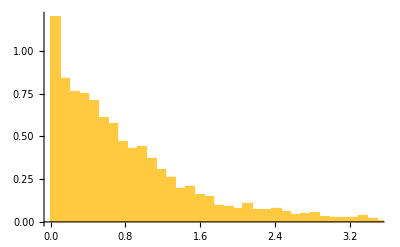

```mathematica
Histogram[s/Mean[s],Automatic,"PDF"]
```

```mathematica
xc=50.;
basis=Basis[xc];reversedBasis=Reverse[basis];
tags=Tag/@basis;
c1=Coin[Pi/4.,xc];
c2=Coin[Pi/6.,xc];

sh=HorizontalShift[xc,tags,reversedBasis];
sv=VerticalShift[xc,tags];

AbsoluteTiming[U=sh.c2.sv.c1]
```

{0.003134,SparseArray[…]}

```mathematica
eigvals=Eigenvalues[U];
```

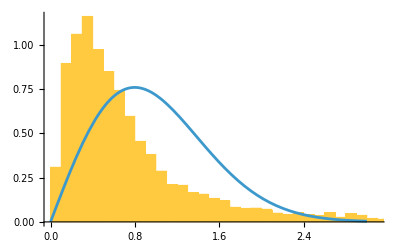

```mathematica
eigphases=Sort[Mod[Arg[#],2Pi]&/@eigvals];
s=Differences[eigphases];
s=s/Mean[s];
Show[Histogram[s,Automatic,"PDF"],Plot[Pi/2s Exp[-Pi s^2/4],{s,0,3}]]
```

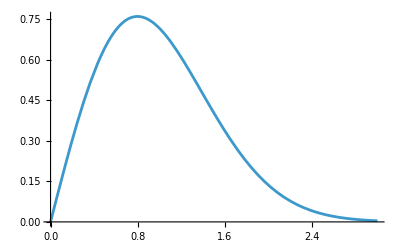

```mathematica
Plot[Pi/2s Exp[-Pi s^2/4],{s,0,3}]
```